```mathematica
path="C:/Coelho_LG/Coelho/Célia/Submodelo/";

NotebookEvaluate[path<>"Exact and near-exact distributions.nb"]

Rat[x_]:=Module[{nn},
If [ToString[Head[x]]!="Real",x,
nn=StringLength[ToString[x,StandardForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

PMFHG[Ns_,r_,ns_,i_,p1_,p2_]:=(Binomial[r,i]*Binomial[Ns-r,ns-i])/(Sum[Binomial[r,j]*Binomial[Ns-r,ns-j],{j,Max[ns+r-Ns,p1+p2+1],Min[ns,r]}])

EVHG[Ns_,r_,ns_,p1_,p2_]:=(Sum[i*Binomial[r,i]*Binomial[Ns-r,ns-i],{i,Max[ns+r-Ns,p1+p2+1],Min[ns,r]}])/(Sum[Binomial[r,i]*Binomial[Ns-r,ns-i],{i,Max[ns+r-Ns,p1+p2+1],Min[ns,r]}])

BisecNRSEven[n_,p1_,p2_,p22_,ai_,bi_,alpha_,eps_:10^-16,prec1_:50,prec2_:20]:=Module[{a,b,c,v1,v2,alph,FC},
a=Rat[ai];b=Rat[bi];
c=(a+b)/2;
alph=Rat[alpha];
v1=SetPrecision[ExCDFNREven[n,p1,p2,p22,a,3*prec1],prec1]-alph;
While[Abs[a-c]>eps,
v2=SetPrecision[ExCDFNREven[n,p1,p2,p22,c,3*prec1],prec1]-alph;
If[v1*v2<0,{b=c},{a=c;v1=v2}];
c=(a+b)/2;
];
SetPrecision[c,prec2]
]

BisecHGEven[Ns_,r_,ns_,p1_,p2_,p22_,ai_,bi_,alpha_,eps_:10^-16,prec1_:50,prec2_:20]:=Module[{a,b,c,v1,v2,alph,FC},
a=Rat[ai];b=Rat[bi];
c=(a+b)/2;
alph=Rat[alpha];
v1=SetPrecision[ExCDFHGEven[Ns,r,ns,p1,p2,p22,a,3*prec1],prec1]-alph;
While[Abs[a-c]>eps,
v2=SetPrecision[ExCDFHGEven[Ns,r,ns,p1,p2,p22,c,3*prec1],prec1]-alph;
If[v1*v2<0,{b=c},{a=c;v1=v2}];
c=(a+b)/2;
];
SetPrecision[c,prec2]
]

NMA[MAT_,p1_,p2_,p22_,d_]:=Module[{AA11,AA22,AA121,AA122,NAA12,p},
p=p1+p2;
AA11=MAT[[1;;(p1+p2-p22),1;;(p1+p2-p22)]];
AA22=MAT[[(p1+p2-p22+1);;(p1+p2),(p1+p2-p22+1);;(p1+p2)]];
AA121=MAT[[1;;(p-p22),(p-p22+1);;p]];
NAA12=d*AA121;
Join[Join[AA11,NAA12,2],Join[Transpose[NAA12],AA22,2]]
]
```

```mathematica
(*** Population covariance matrix for the set of p=p1+p2 variables ***)
SIG={{17.2,-9.3,22.1,-5.9,-3.8,0.2,0.6,9.4,-0.4,-12.2,-2.8,7.9,9.4,4.7,12.8,-6.2},{-9.3,29.2,-6.9,10.6,19.1,-3.2,8.2,-6.9,0.8,8.,6.1,-7.,-2.,0.3,5.5,19.},{22.1,-6.9,69.4,-22.6,-15.7,6.7,-1.3,5.3,7.,-23.3,5.7,-16.1,13.8,6.9,38.3,-13.1},{-5.9,10.6,-22.6,14.5,13.9,-2.8,3.1,-1.1,-5.2,7.1,0.2,8.2,0.,0.2,-7.8,10.7},{-3.8,19.1,-15.7,13.9,20.7,-6.3,6.9,0.1,-2.6,5.2,-0.1,6.4,1.6,0.8,0.,17.6},{0.2,-3.2,6.7,-2.8,-6.3,14.6,-4.,-5.6,0.3,0.6,1.9,0.2,-5.7,2.,-0.6,-14.},{0.6,8.2,-1.3,3.1,6.9,-4.,10.7,2.6,4.9,3.4,0.8,0.5,6.5,5.9,1.7,4.9},{9.4,-6.9,5.3,-1.1,0.1,-5.6,2.6,11.1,-1.,-6.4,-2.6,4.5,10.1,2.4,3.1,1.8},{-0.4,0.8,7.,-5.2,-2.6,0.3,4.9,-1.,12.3,2.1,-0.1,-6.1,2.5,5.,3.1,-5.4},{-12.2,8.,-23.3,7.1,5.2,0.6,3.4,-6.4,2.1,13.9,0.2,1.8,-7.8,-0.1,-12.8,1.6},{-2.8,6.1,5.7,0.2,-0.1,1.9,0.8,-2.6,-0.1,0.2,7.1,-11.,3.7,1.1,4.1,2.7},{7.9,-7.,-16.1,8.2,6.4,0.2,0.5,4.5,-6.1,1.8,-11.,34.9,-6.4,1.1,-7.9,-4.7},{9.4,-2.,13.8,0.,1.6,-5.7,6.5,10.1,2.5,-7.8,3.7,-6.4,24.6,8.9,10.5,1.6},{4.7,0.3,6.9,0.2,0.8,2.,5.9,2.4,5.,-0.1,1.1,1.1,8.9,8.8,4.7,-5.9},{12.8,5.5,38.3,-7.8,0.,-0.6,1.7,3.1,3.1,-12.8,4.1,-7.9,10.5,4.7,27.3,1.},{-6.2,19.,-13.1,10.7,17.6,-14.,4.9,1.8,-5.4,1.6,2.7,-4.7,1.6,-5.9,1.,28.8}};
```

```mathematica
MatrixForm[SIG]
```

(17.2 | -9.3 | 22.1 | -5.9 | -3.8 | 0.2 | 0.6 | 9.4 | -0.4 | -12.2 | -2.8 | 7.9 | 9.4 | 4.7 | 12.8 | -6.2
-9.3 | 29.2 | -6.9 | 10.6 | 19.1 | -3.2 | 8.2 | -6.9 | 0.8 | 8. | 6.1 | -7. | -2. | 0.3 | 5.5 | 19.
22.1 | -6.9 | 69.4 | -22.6 | -15.7 | 6.7 | -1.3 | 5.3 | 7. | -23.3 | 5.7 | -16.1 | 13.8 | 6.9 | 38.3 | -13.1
-5.9 | 10.6 | -22.6 | 14.5 | 13.9 | -2.8 | 3.1 | -1.1 | -5.2 | 7.1 | 0.2 | 8.2 | 0. | 0.2 | -7.8 | 10.7
-3.8 | 19.1 | -15.7 | 13.9 | 20.7 | -6.3 | 6.9 | 0.1 | -2.6 | 5.2 | -0.1 | 6.4 | 1.6 | 0.8 | 0. | 17.6
0.2 | -3.2 | 6.7 | -2.8 | -6.3 | 14.6 | -4. | -5.6 | 0.3 | 0.6 | 1.9 | 0.2 | -5.7 | 2. | -0.6 | -14.
0.6 | 8.2 | -1.3 | 3.1 | 6.9 | -4. | 10.7 | 2.6 | 4.9 | 3.4 | 0.8 | 0.5 | 6.5 | 5.9 | 1.7 | 4.9
9.4 | -6.9 | 5.3 | -1.1 | 0.1 | -5.6 | 2.6 | 11.1 | -1. | -6.4 | -2.6 | 4.5 | 10.1 | 2.4 | 3.1 | 1.8
-0.4 | 0.8 | 7. | -5.2 | -2.6 | 0.3 | 4.9 | -1. | 12.3 | 2.1 | -0.1 | -6.1 | 2.5 | 5. | 3.1 | -5.4
-12.2 | 8. | -23.3 | 7.1 | 5.2 | 0.6 | 3.4 | -6.4 | 2.1 | 13.9 | 0.2 | 1.8 | -7.8 | -0.1 | -12.8 | 1.6
-2.8 | 6.1 | 5.7 | 0.2 | -0.1 | 1.9 | 0.8 | -2.6 | -0.1 | 0.2 | 7.1 | -11. | 3.7 | 1.1 | 4.1 | 2.7
7.9 | -7. | -16.1 | 8.2 | 6.4 | 0.2 | 0.5 | 4.5 | -6.1 | 1.8 | -11. | 34.9 | -6.4 | 1.1 | -7.9 | -4.7
9.4 | -2. | 13.8 | 0. | 1.6 | -5.7 | 6.5 | 10.1 | 2.5 | -7.8 | 3.7 | -6.4 | 24.6 | 8.9 | 10.5 | 1.6
4.7 | 0.3 | 6.9 | 0.2 | 0.8 | 2. | 5.9 | 2.4 | 5. | -0.1 | 1.1 | 1.1 | 8.9 | 8.8 | 4.7 | -5.9
12.8 | 5.5 | 38.3 | -7.8 | 0. | -0.6 | 1.7 | 3.1 | 3.1 | -12.8 | 4.1 | -7.9 | 10.5 | 4.7 | 27.3 | 1.
-6.2 | 19. | -13.1 | 10.7 | 17.6 | -14. | 4.9 | 1.8 | -5.4 | 1.6 | 2.7 | -4.7 | 1.6 | -5.9 | 1. | 28.8)

```mathematica
(*** Inspection of valid delta values for the covariance matrix ***)
p1=5;
p2=11;
p22=4;
sup=1.1;
step=.1;
Table[PositiveDefiniteMatrixQ[NMA[SIG,p1,p2,p22,d]],{d,0,sup,step}]
sup=sup-1*step;
```

{True,True,True,True,True,True,True,True,True,True,True,False}

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=50, r= 25, ns=40 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=50;
r= 25;
ns=40;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

25

20.0216

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05,10^-20]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01,10^-20]
```

0.0024388932446661820622

0.00021235438157140676043

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0492,0.0529,0.0479,0.0501,0.0561,0.0593,0.0705,0.0905,0.1313,0.1706,0.2121,0.2663,0.3377,0.5062,0.785,0.9994}

{0.0103,0.0103,0.0088,0.01,0.0105,0.0116,0.0129,0.015,0.0236,0.0261,0.0364,0.0437,0.0545,0.0976,0.2161,0.9123}

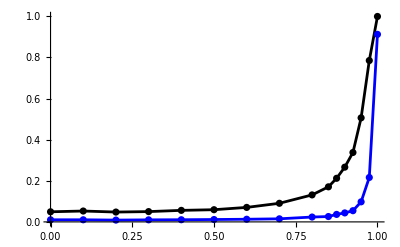

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=20;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.0075581343683622512819

0.0027154721714491296403

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0492,0.0497,0.0501,0.0577,0.0666,0.0783,0.0996,0.141,0.2531,0.3468,0.4275,0.5215,0.6622,0.8174,0.9623,1.}

{0.0095,0.0112,0.0094,0.0113,0.0144,0.0179,0.0231,0.0362,0.076,0.1252,0.1655,0.2272,0.3397,0.5194,0.8145,0.9997}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0492,0.0529,0.0479,0.0501,0.0561,0.0593,0.0705,0.0905,0.1313,0.1706,0.2121,0.2663,0.3377,0.5062,0.785,0.9994};
P01={0.0103,0.0103,0.0088,0.01,0.0105,0.0116,0.0129,0.015,0.0236,0.0261,0.0364,0.0437,0.0545,0.0976,0.2161,0.9123};
```

```mathematica
P05nr={0.0492,0.0497,0.0501,0.0577,0.0666,0.0783,0.0996,0.141,0.2531,0.3468,0.4275,0.5215,0.6622,0.8174,0.9623,1.};
P01nr={0.0095,0.0112,0.0094,0.0113,0.0144,0.0179,0.0231,0.0362,0.076,0.1252,0.1655,0.2272,0.3397,0.5194,0.8145,0.9997};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 50, ",Style["r",Italic]," = 25, ",Superscript[Style["n",Italic],"*"]," = 40 ",Style["(n",Italic]," = 20)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=50, r= 40, ns=22 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=50;
r=40;
ns=22;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

22

18.1465

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.00008291991985954210233

3.1954540121358605601×10^-6

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0512,0.0526,0.0522,0.0514,0.0549,0.0595,0.0642,0.072,0.087,0.1117,0.1211,0.1447,0.173,0.2402,0.368,0.8996}

{0.0098,0.0103,0.0085,0.0112,0.0106,0.0126,0.0122,0.0154,0.0185,0.0227,0.0243,0.0304,0.0378,0.0511,0.0812,0.3679}

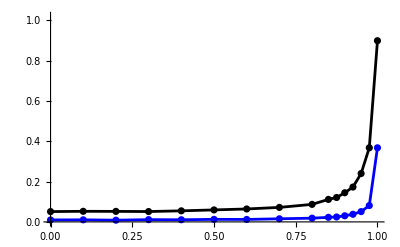

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=18;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,10^-10,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,10^-10,0.99,0.01]
```

0.00048039234896106074532

0.000081409968344220684713

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0507,0.0518,0.0489,0.0516,0.0575,0.0629,0.0766,0.1002,0.1418,0.1844,0.2175,0.2653,0.3406,0.4682,0.7076,0.9947}

{0.0089,0.0099,0.0095,0.0109,0.0117,0.013,0.0163,0.0205,0.0341,0.0455,0.0575,0.0779,0.1027,0.1668,0.332,0.9105}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0512,0.0526,0.0522,0.0514,0.0549,0.0595,0.0642,0.072,0.087,0.1117,0.1211,0.1447,0.173,0.2402,0.368,0.8996};
P01={0.0098,0.0103,0.0085,0.0112,0.0106,0.0126,0.0122,0.0154,0.0185,0.0227,0.0243,0.0304,0.0378,0.0511,0.0812,0.3679};
```

```mathematica
P05nr={0.0507,0.0518,0.0489,0.0516,0.0575,0.0629,0.0766,0.1002,0.1418,0.1844,0.2175,0.2653,0.3406,0.4682,0.7076,0.9947};
P01nr={0.0089,0.0099,0.0095,0.0109,0.0117,0.013,0.0163,0.0205,0.0341,0.0455,0.0575,0.0779,0.1027,0.1668,0.332,0.9105};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 50, ",Style["r",Italic]," = 40, ",Superscript[Style["n",Italic],"*"]," = 22 ",Style["(n",Italic]," = 18)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]
},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=50, r= 30, ns=30 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=50;
r=30;
ns=30;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

30

18.578

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.00014408976403144719959

5.5959023818435951956×10^-6

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
p1=5;
p2=11;
p22=4;
Ns=50;
r=30;
ns=30;
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0487,0.0512,0.0539,0.0541,0.0543,0.056,0.0608,0.0719,0.0906,0.1077,0.121,0.1419,0.1757,0.2297,0.3819,0.9276}

{0.009,0.0109,0.0111,0.0113,0.0098,0.0121,0.0126,0.0129,0.0183,0.0216,0.026,0.0291,0.0399,0.0494,0.0862,0.3867}

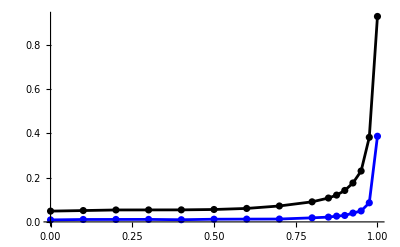

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=19;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.002694984895707411271

0.00074800724453824375959

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0506,0.0476,0.0516,0.0579,0.0618,0.0706,0.0884,0.1255,0.1899,0.2613,0.3205,0.4045,0.5137,0.6763,0.8886,0.9999}

{0.0102,0.011,0.0105,0.0115,0.0123,0.0136,0.0193,0.0284,0.0518,0.0784,0.1034,0.145,0.2125,0.3408,0.6123,0.996}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0487,0.0512,0.0539,0.0541,0.0543,0.056,0.0608,0.0719,0.0906,0.1077,0.121,0.1419,0.1757,0.2297,0.3819,0.9276};
P01={0.009,0.0109,0.0111,0.0113,0.0098,0.0121,0.0126,0.0129,0.0183,0.0216,0.026,0.0291,0.0399,0.0494,0.0862,0.3867};
P05nr={0.0506,0.0476,0.0516,0.0579,0.0618,0.0706,0.0884,0.1255,0.1899,0.2613,0.3205,0.4045,0.5137,0.6763,0.8886,0.9999};
P01nr={0.0102,0.011,0.0105,0.0115,0.0123,0.0136,0.0193,0.0284,0.0518,0.0784,0.1034,0.145,0.2125,0.3408,0.6123,0.996};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 50, ",Style["r",Italic]," = 30, ",Superscript[Style["n",Italic],"*"]," = 30 ",Style["(n",Italic]," = 19)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=50, r= 40, ns=40 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=50;
r=40;
ns=40;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

30

40

32.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.18437754586948833145

0.13062268330807031074

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0511,0.0526,0.0667,0.0825,0.1157,0.1841,0.3096,0.5173,0.8244,0.9957,1.}

{0.0118,0.0117,0.0149,0.0179,0.0323,0.0526,0.1149,0.2558,0.5789,0.9673,1.}

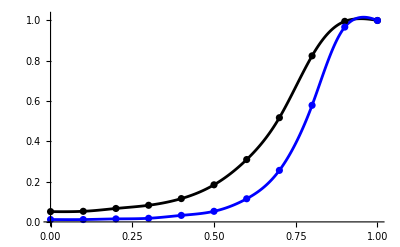

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=32;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.1882050119351707212

0.13534074053763755729

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0474,0.0541,0.0602,0.0802,0.1145,0.1915,0.3006,0.5357,0.8225,0.994,1.}

{0.009,0.0113,0.0118,0.0194,0.0293,0.0606,0.116,0.2768,0.5992,0.9689,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0511,0.0526,0.0667,0.0825,0.1157,0.1841,0.3096,0.5173,0.8244,0.9957,1.};
P01={0.0118,0.0117,0.0149,0.0179,0.0323,0.0526,0.1149,0.2558,0.5789,0.9673,1.};
P05nr={0.0474,0.0541,0.0602,0.0802,0.1145,0.1915,0.3006,0.5357,0.8225,0.994,1.};
P01nr={0.009,0.0113,0.0118,0.0194,0.0293,0.0606,0.116,0.2768,0.5992,0.9689,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 50, ",Style["r",Italic]," = 40, ",Superscript[Style["n",Italic],"*"]," = 40 ",Style["(n",Italic]," = 32)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 50, ns=60 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=100;
r=50;
ns=60;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

50

30.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.13245230598289121229

0.079845953004706842642

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0474,0.0529,0.0629,0.0661,0.0889,0.1336,0.2114,0.3779,0.6765,0.9734,1.}

{0.0095,0.0105,0.0126,0.0136,0.0177,0.0305,0.054,0.1319,0.3394,0.8428,1.}

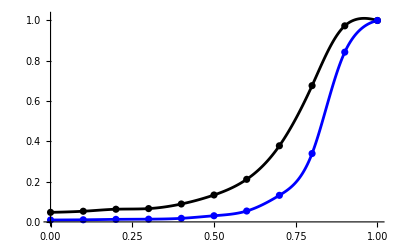

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=30;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.15387769462044121456

0.10626800447527629067

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
ist={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0473,0.0529,0.0573,0.0775,0.1056,0.1645,0.2779,0.4625,0.7712,0.989,1.}

{0.01,0.0112,0.013,0.0171,0.0279,0.0461,0.1008,0.2133,0.516,0.9389,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0474,0.0529,0.0629,0.0661,0.0889,0.1336,0.2114,0.3779,0.6765,0.9734,1.};
P01={0.0095,0.0105,0.0126,0.0136,0.0177,0.0305,0.054,0.1319,0.3394,0.8428,1.};
P05nr={0.0473,0.0529,0.0573,0.0775,0.1056,0.1645,0.2779,0.4625,0.7712,0.989,1.};
P01nr={0.01,0.0112,0.013,0.0171,0.0279,0.0461,0.1008,0.2133,0.516,0.9389,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 50, ",Superscript[Style["n",Italic],"*"]," = 60 ",Style["(n",Italic]," = 30)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2
,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 85, ns=60 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=100;
r=85;
ns=60;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

45

60

51.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.43400730678242831123

0.3671828194582185858

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0487,0.0587,0.0794,0.1244,0.2194,0.3947,0.6602,0.9182,0.9965,1.,1.}

{0.0101,0.0125,0.0191,0.0367,0.0764,0.1791,0.4054,0.7617,0.9776,1.,1.}

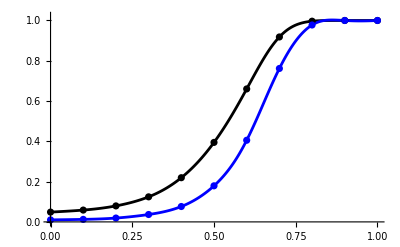

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=51;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.43662256973566052619

0.37106341842078723367

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0507,0.0582,0.077,0.1219,0.2337,0.408,0.6743,0.9138,0.9967,1.,1.}

{0.0088,0.0132,0.0171,0.0337,0.0818,0.1874,0.4211,0.764,0.9797,1.,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0487,0.0587,0.0794,0.1244,0.2194,0.3947,0.6602,0.9182,0.9965,1.,1.};
P01={0.0101,0.0125,0.0191,0.0367,0.0764,0.1791,0.4054,0.7617,0.9776,1.,1.};
P05nr={0.0507,0.0582,0.077,0.1219,0.2337,0.408,0.6743,0.9138,0.9967,1.,1.};
P01nr={0.0088,0.0132,0.0171,0.0337,0.0818,0.1874,0.4211,0.764,0.9797,1.,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 85, ",Superscript[Style["n",Italic],"*"]," = 60 ",Style["(n",Italic]," = 51)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 50, ns=80 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=100;
r=50;
ns=80;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

30

50

40.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.30367010945206773674

0.23707014484407294077

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0501,0.0505,0.0639,0.0963,0.1519,0.2665,0.4426,0.7232,0.9543,0.9999,1.}

{0.01,0.009,0.0143,0.0263,0.0441,0.0961,0.2089,0.4592,0.8384,0.9984,1.}

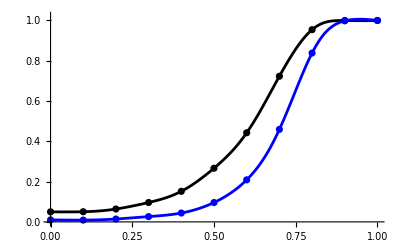

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=40;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.31060815945030863733

0.2467977167469408424

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0517,0.0559,0.0654,0.1021,0.1661,0.2795,0.4808,0.7549,0.9606,0.9999,1.}

{0.0098,0.0129,0.014,0.0288,0.0498,0.105,0.2333,0.5095,0.8665,0.9993,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0501,0.0505,0.0639,0.0963,0.1519,0.2665,0.4426,0.7232,0.9543,0.9999,1.};
P01={0.01,0.009,0.0143,0.0263,0.0441,0.0961,0.2089,0.4592,0.8384,0.9984,1.};
P05nr={0.0517,0.0559,0.0654,0.1021,0.1661,0.2795,0.4808,0.7549,0.9606,0.9999,1.};
P01nr={0.0098,0.0129,0.014,0.0288,0.0498,0.105,0.2333,0.5095,0.8665,0.9993,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 50, ",Superscript[Style["n",Italic],"*"]," = 80 ",Style["(n",Italic]," = 40)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 25, ns=80 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=100;
r=25;
ns=80;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

25

20.1103

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.001718446578915816259

0.000099437197722129280604

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0455,0.0479,0.0529,0.048,0.0561,0.0596,0.0629,0.0869,0.1123,0.1403,0.1717,0.2148,0.2827,0.4222,0.6807,0.9991}

{0.0092,0.0102,0.0087,0.0097,0.0094,0.0107,0.0112,0.0156,0.0196,0.0238,0.0286,0.0333,0.0424,0.0698,0.1354,0.7733}

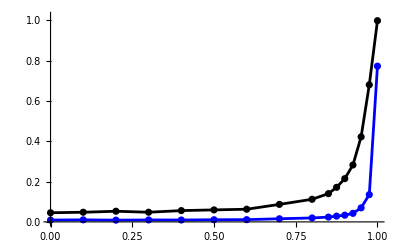

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=20;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.0075581343683622512819

0.0027154721714491296403

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0492,0.0502,0.0555,0.0627,0.0719,0.0811,0.1066,0.148,0.2418,0.3483,0.4197,0.5221,0.6564,0.8235,0.9636,1.}

{0.0096,0.0104,0.0127,0.013,0.0153,0.0174,0.0262,0.0389,0.0734,0.1246,0.1709,0.2308,0.34,0.529,0.8224,0.9999}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0455,0.0479,0.0529,0.048,0.0561,0.0596,0.0629,0.0869,0.1123,0.1403,0.1717,0.2148,0.2827,0.4222,0.6807,0.9991};
P01={0.0092,0.0102,0.0087,0.0097,0.0094,0.0107,0.0112,0.0156,0.0196,0.0238,0.0286,0.0333,0.0424,0.0698,0.1354,0.7733};
P05nr={0.0492,0.0502,0.0555,0.0627,0.0719,0.0811,0.1066,0.148,0.2418,0.3483,0.4197,0.5221,0.6564,0.8235,0.9636,1.};
P01nr={0.0096,0.0104,0.0127,0.013,0.0153,0.0174,0.0262,0.0389,0.0734,0.1246,0.1709,0.2308,0.34,0.529,0.8224,0.9999};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 25, ",Superscript[Style["n",Italic],"*"]," = 80 ",Style["(n",Italic]," = 20)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 80, ns=30 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=100;
r=80;
ns=30;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

30

24.0003

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.036351693315624604336

0.013449949680306899669

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0512,0.0546,0.0511,0.0593,0.0682,0.0883,0.1175,0.1778,0.3378,0.4823,0.5859,0.7285,0.858,0.9625,0.999,1.}

{0.0109,0.0117,0.0117,0.014,0.0138,0.0178,0.0204,0.0397,0.0851,0.1503,0.2106,0.3114,0.4739,0.7239,0.9592,1.}

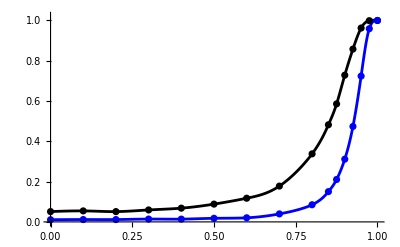

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=24;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.052477964249575633665

0.02905358625727270086

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0541,0.055,0.0554,0.0648,0.0867,0.1127,0.1635,0.2665,0.4899,0.6531,0.7547,0.867,0.9468,0.9889,0.9999,1.}

{0.0119,0.0107,0.0113,0.0134,0.02,0.0288,0.0454,0.0923,0.216,0.3658,0.4765,0.6364,0.7961,0.9378,0.9969,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0512,0.0546,0.0511,0.0593,0.0682,0.0883,0.1175,0.1778,0.3378,0.4823,0.5859,0.7285,0.858,0.9625,0.999,1.};
P01={0.0109,0.0117,0.0117,0.014,0.0138,0.0178,0.0204,0.0397,0.0851,0.1503,0.2106,0.3114,0.4739,0.7239,0.9592,1.};
P05nr={0.0541,0.055,0.0554,0.0648,0.0867,0.1127,0.1635,0.2665,0.4899,0.6531,0.7547,0.867,0.9468,0.9889,0.9999,1.};
P01nr={0.0119,0.0107,0.0113,0.0134,0.02,0.0288,0.0454,0.0923,0.216,0.3658,0.4765,0.6364,0.7961,0.9378,0.9969,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 80, ",Superscript[Style["n",Italic],"*"]," = 30 ",Style["(n",Italic]," = 24)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 90, ns=70 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=150;
r=90;
ns=70;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

70

42.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.32326490819328791843

0.25233828151306527558

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0469,0.0524,0.0649,0.0949,0.1439,0.26,0.4511,0.7441,0.9643,1.,1.}

{0.0079,0.0109,0.0136,0.0231,0.0393,0.0877,0.1968,0.4541,0.8558,0.9997,1.}

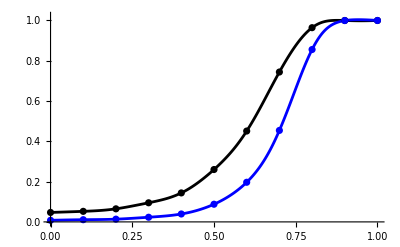

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=42;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.33693947638704418822

0.27206672523437968704

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0501,0.0558,0.0688,0.1066,0.1757,0.2962,0.5217,0.7924,0.9755,0.9999,1.}

{0.0099,0.0114,0.0157,0.0277,0.0558,0.1132,0.2653,0.5611,0.9031,0.9997,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0469,0.0524,0.0649,0.0949,0.1439,0.26,0.4511,0.7441,0.9643,1.,1.};
P01={0.0079,0.0109,0.0136,0.0231,0.0393,0.0877,0.1968,0.4541,0.8558,0.9997,1.};
P05nr={0.0501,0.0558,0.0688,0.1066,0.1757,0.2962,0.5217,0.7924,0.9755,0.9999,1.};
P01nr={0.0099,0.0114,0.0157,0.0277,0.0558,0.1132,0.2653,0.5611,0.9031,0.9997,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 90, ",Superscript[Style["n",Italic],"*"]," = 70 ",Style["(n",Italic]," = 42)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 120, ns=100 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=150;
r=120;
ns=100;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

70

100

80.

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.62432858056955875984

0.56865048449941288726

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0489,0.0652,0.1111,0.2103,0.4314,0.7156,0.9401,0.9972,1.,1.,1.}

{0.0104,0.0137,0.0277,0.0712,0.2101,0.472,0.8231,0.9865,1.,1.,1.}

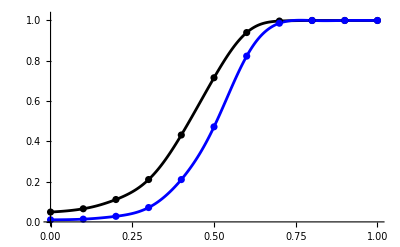

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=80;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.62550659704752392223

0.57052498193734843804

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
t={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0502,0.061,0.1085,0.2181,0.4294,0.7208,0.9411,0.9988,1.,1.,1.}

{0.0092,0.0116,0.0306,0.0746,0.2015,0.4888,0.8319,0.9912,1.,1.,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
t={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0489,0.0652,0.1111,0.2103,0.4314,0.7156,0.9401,0.9972,1.,1.,1.};
P01={0.0104,0.0137,0.0277,0.0712,0.2101,0.472,0.8231,0.9865,1.,1.,1.};
P05nr={0.0502,0.061,0.1085,0.2181,0.4294,0.7208,0.9411,0.9988,1.,1.,1.};
P01nr={0.0092,0.0116,0.0306,0.0746,0.2015,0.4888,0.8319,0.9912,1.,1.,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->4,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 120, ",Superscript[Style["n",Italic],"*"]," = 100 ",Style["(n",Italic]," = 80)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 30, ns=100 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=150;
r=30;
ns=100;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

30

20.3293

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.0011541977621928553931

0.000051952358009459032723

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0514,0.0504,0.0534,0.05,0.0544,0.0626,0.065,0.0773,0.0937,0.1215,0.1392,0.1727,0.2206,0.3181,0.5642,0.9963}

{0.0096,0.0106,0.0127,0.0093,0.0106,0.013,0.0146,0.0164,0.0194,0.0216,0.0264,0.031,0.0387,0.056,0.1007,0.6047}

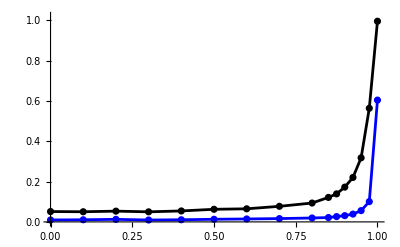

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=20;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.0075581343683622512819

0.0027154721714491296403

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0491,0.0485,0.0554,0.06,0.0683,0.0819,0.1019,0.1518,0.2517,0.3514,0.4175,0.5182,0.6507,0.8216,0.9612,1.}

{0.009,0.0107,0.0106,0.0138,0.0142,0.0183,0.0236,0.0393,0.0818,0.1235,0.1566,0.2215,0.3285,0.5258,0.8153,0.9995}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.0514,0.0504,0.0534,0.05,0.0544,0.0626,0.065,0.0773,0.0937,0.1215,0.1392,0.1727,0.2206,0.3181,0.5642,0.9963};
P01={0.0096,0.0106,0.0127,0.0093,0.0106,0.013,0.0146,0.0164,0.0194,0.0216,0.0264,0.031,0.0387,0.056,0.1007,0.6047};
P05nr={0.0491,0.0485,0.0554,0.06,0.0683,0.0819,0.1019,0.1518,0.2517,0.3514,0.4175,0.5182,0.6507,0.8216,0.9612,1.};
P01nr={0.009,0.0107,0.0106,0.0138,0.0142,0.0183,0.0236,0.0393,0.0818,0.1235,0.1566,0.2215,0.3285,0.5258,0.8153,0.9995};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 30, ",Superscript[Style["n",Italic],"*"]," = 100 ",Style["(n",Italic]," = 20)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 90, ns=30 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=150;
r=90;
ns=30;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

30

19.086

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.00020849637690443589522

7.9797255965242295862×10^-6

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.05,0.0485,0.0492,0.0513,0.0575,0.0549,0.0646,0.067,0.0858,0.1076,0.1197,0.1441,0.1732,0.235,0.3805,0.9378}

{0.0107,0.0101,0.0101,0.0115,0.0123,0.0122,0.0134,0.0131,0.0189,0.0208,0.026,0.0276,0.036,0.0484,0.0844,0.3875}

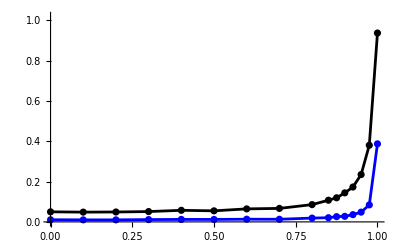

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=19;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.002694984895707411271

0.00074800724453824375959

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0533,0.0507,0.0538,0.0566,0.0625,0.0696,0.089,0.1225,0.1932,0.267,0.3215,0.3946,0.5117,0.6729,0.8923,0.9998}

{0.0108,0.0096,0.011,0.0112,0.0138,0.0151,0.0189,0.0305,0.0499,0.0815,0.1033,0.1383,0.2101,0.339,0.6175,0.996}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

```mathematica
P05={0.05,0.0485,0.0492,0.0513,0.0575,0.0549,0.0646,0.067,0.0858,0.1076,0.1197,0.1441,0.1732,0.235,0.3805,0.9378};
P01={0.0107,0.0101,0.0101,0.0115,0.0123,0.0122,0.0134,0.0131,0.0189,0.0208,0.026,0.0276,0.036,0.0484,0.0844,0.3875};
P05nr={0.0533,0.0507,0.0538,0.0566,0.0625,0.0696,0.089,0.1225,0.1932,0.267,0.3215,0.3946,0.5117,0.6729,0.8923,0.9998};
P01nr={0.0108,0.0096,0.011,0.0112,0.0138,0.0151,0.0189,0.0305,0.0499,0.0815,0.1033,0.1383,0.2101,0.339,0.6175,0.996};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->1,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 90, ",Superscript[Style["n",Italic],"*"]," = 30 ",Style["(n",Italic]," = 19)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->1,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 100, ns=80 *)
```

```mathematica
(*** Computation of the possible random sample size values and Mean Value of the truncated Hypergeometric distribution for sampe sizes  ***)

p1=5;
p2=11;
p22=4;
Ns=150;
r=100;
ns=80;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

30

80

53.3333

```mathematica
(*** Computation of the exact 0.05 and 0.01 quantiles ***)

q05=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.05]
q01=BisecHGEven[Ns,r,ns,p1,p2,p22,10^-10,1-10^-10,.01]
```

0.45188942802999407817

0.38357219020001545

```mathematica
(*** Computations for Power ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05={};
P01=P05;
Do[Mat=NMA[SIG,p1,p2,p22,d];
TT=Flatten[Table[RandomInteger[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]],1],{i,1,nv}]];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],TT[[i]]];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05=Append[P05,N[Count[L,x_/;x<q05]/nv]];
P01=Append[P01,N[Count[L,x_/;x<q01]/nv]],{d,list}]
P05
P01
```

{0.0523,0.0622,0.0809,0.133,0.2348,0.4277,0.6941,0.9286,0.9983,1.,1.}

{0.0104,0.0126,0.019,0.039,0.0847,0.1989,0.4354,0.7762,0.984,1.,1.}

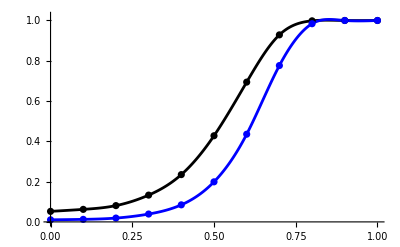

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->All];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=53;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
q01nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.01]
```

0.45518253387434571283

0.39002178430453844261

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
nv=10000;
P05nr={};
P01nr=P05nr;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]];
P01nr=Append[P01nr,N[Count[L,x_/;x<q01nr]/nv]],{d,list}]
P05nr
P01nr
```

{0.0492,0.0537,0.0809,0.1403,0.2422,0.4384,0.7054,0.9325,0.9977,1.,1.}

{0.0098,0.0122,0.019,0.0419,0.0901,0.2087,0.4548,0.805,0.9866,1.,1.}

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

```mathematica
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
P05={0.0523,0.0622,0.0809,0.133,0.2348,0.4277,0.6941,0.9286,0.9983,1.,1.};
P01={0.0104,0.0126,0.019,0.039,0.0847,0.1989,0.4354,0.7762,0.984,1.,1.};
P05nr={0.0492,0.0537,0.0809,0.1403,0.2422,0.4384,0.7054,0.9325,0.9977,1.,1.};
P01nr={0.0098,0.0122,0.019,0.0419,0.0901,0.2087,0.4548,0.805,0.9866,1.,1.};
```

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 100, ",Superscript[Style["n",Italic],"*"]," = 80 ",Style["(n",Italic]," = 53)"}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01[[i]]},{i,1,Length[list]}]},PlotStyle->{Black,Blue}];
plot3=ListPlot[{Table[{list[[i]],P05nr[[i]]},{i,1,Length[list]}],Table[{list[[i]],P01nr[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->2,PlotStyle->{{Dotted,Black,Thickness[0.005]},{Dotted,Blue,Thickness[0.005]}},PlotRange->All];
Show[plot1,plot2,plot3]
```

```mathematica
(*** Different non-random sample sizes compared with a given Hypergeometric  ***)
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=50, r= 40, ns=40 *)
```

```mathematica
p1=5;
p2=11;
p22=4;
Ns=50;
r=40;
ns=40;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

30

40

32.

```mathematica
P05={0.0511,0.0526,0.0667,0.0825,0.1157,0.1841,0.3096,0.5173,0.8244,0.9957,1.};
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
(*** Plots of power ***)
```

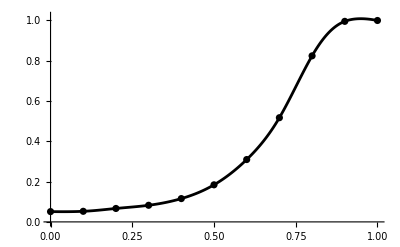

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];

plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=32;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
P05nr32={0.0474,0.0541,0.0602,0.0802,0.1145,0.1915,0.3006,0.5357,0.8225,0.994,1.};
```

0.1882050119351707212

```mathematica
n=40;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.31060815945030863733

```mathematica
n=47;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.39583171081678550723

```mathematica
n=28;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.11894034791726494689

```mathematica
n=20;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.0075581343683621566057

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
P05nr={};
nv=10000;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]],{d,list}]
P05nr
```

{0.048,0.0522,0.0629,0.0791,0.1161,0.1889,0.3129,0.5299,0.8405,0.9946,1.}

```mathematica
P05nr40={0.0496,0.0512,0.0687,0.0945,0.1574,0.2755,0.4824,0.748,0.9584,1.,1.};
P05nr47={0.0504,0.0523,0.0818,0.1163,0.2058,0.3649,0.6132,0.8651,0.9914,1.,1.};
P05nr28={0.0517,0.0534,0.0564,0.0769,0.1005,0.1442,0.2358,0.3983,0.6896,0.9685,1.};
P05nr20={0.0483,0.055,0.0508,0.0606,0.0668,0.0773,0.1029,0.1446,0.2529,0.5209,1.};
```

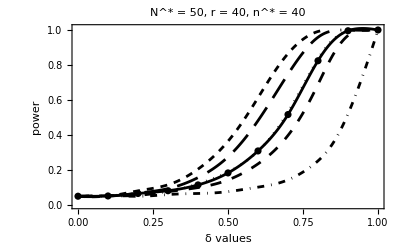

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.01},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 50, ",Style["r",Italic]," = 40, ",Superscript[Style["n",Italic],"*"]," = 40 "}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}];
plot3=ListPlot[{Table[{list[[i]],P05nr20[[i]]},{i,1,Length[list]}],
Table[{list[[i]],P05nr28[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr32[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr40[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr47[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->5,PlotStyle->{{DotDashed,Black,Thickness[0.005]},{Dashing[{.02,.02}],Black,Thickness[0.005]},{Dotted,Black,Thickness[0.005]},{Dashing[{.04,.02}],Black,Thickness[0.005]},{Dashed,Black,Thickness[0.005]}},PlotRange->All];
Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=100, r= 80, ns=30 *)
```

```mathematica
p1=5;
p2=11;
p22=4;
Ns=100;
r=80;
ns=30;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

30

24.0003

```mathematica
P05={0.0512,0.0546,0.0511,0.0593,0.0682,0.0883,0.1175,0.1778,0.3378,0.4823,0.5859,0.7285,0.858,0.9625,0.999,1.};
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.85,.875,.9,.925,.95,.975,1};
```

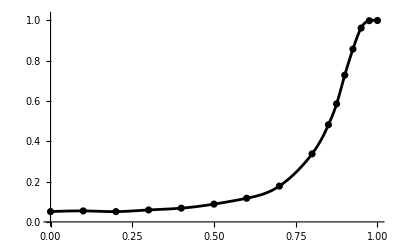

```mathematica
(*** Plots of power ***)
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}]
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}]
Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=24;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
P05nr24={0.0541,0.055,0.0554,0.0648,0.0867,0.1127,0.1635,0.2665,0.4899,0.6531,0.7547,0.867,0.9468,0.9889,0.9999,1.};
```

0.052477964249575633665

```mathematica
n=30;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.15387769462044121456

```mathematica
n=50;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.42690163463909064882

```mathematica
n=18;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.00048039234896111571757

```mathematica
n=20;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.0075581343683621566057

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
P05nr={};
nv=10000;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]],{d,list}]
P05nr
```

{0.0542,0.0515,0.0556,0.058,0.0635,0.0768,0.1018,0.151,0.2479,0.3511,0.4231,0.5258,0.6565,0.8167,0.9638,1.}

```mathematica
P05nr30={0.0555,0.0504,0.0568,0.0795,0.1139,0.1772,0.274,0.4724,0.7747,0.9102,0.9591,0.988,0.9966,0.9997,1.,1.};
P05nr50={0.0494,0.0583,0.0745,0.123,0.2265,0.3993,0.6598,0.9078,0.996,0.9997,1.,1.,1.,1.,1.,1.};
P05nr18={0.0532,0.0502,0.0517,0.0562,0.0631,0.0623,0.0771,0.0936,0.143,0.1725,0.2112,0.2709,0.3448,0.4706,0.7012,0.9957};
P05nr20={0.0542,0.0515,0.0556,0.058,0.0635,0.0768,0.1018,0.151,0.2479,0.3511,0.4231,0.5258,0.6565,0.8167,0.9638,1.};
```

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

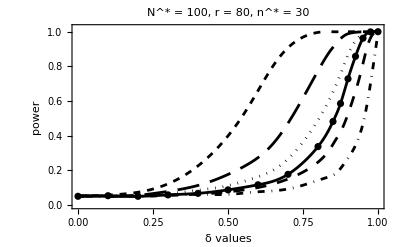

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 100, ",Style["r",Italic]," = 80, ",Superscript[Style["n",Italic],"*"]," = 30 "}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}];
plot3=ListPlot[{Table[{list[[i]],P05nr18[[i]]},{i,1,Length[list]}],
Table[{list[[i]],P05nr20[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr24[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr30[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr50[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->6,PlotStyle->{{DotDashed,Black,Thickness[0.005]},{Dashing[{.02,.02}],Black,Thickness[0.005]},{Dotted,Black,Thickness[0.005]},{Dashing[{.04,.02}],Black,Thickness[0.005]},{Dashed,Black,Thickness[0.005]}},PlotRange->All];
Show[plot1,plot2,plot3]
```

```mathematica
(* Truncated Hypergeometric distribution for sample size with Ns=150, r= 90, ns=70 *)
```

```mathematica
p1=5;
p2=11;
p22=4;
Ns=150;
r=90;
ns=70;
Max[ns+r-Ns,p1+p2+1]
Min[ns,r]
N[Mean[TruncatedDistribution[{Max[ns+r-Ns,p1+p2+1]-1,Min[ns,r]+1},HypergeometricDistribution[ns,r,Ns]]]]
```

17

70

42.

```mathematica
P05={0.0469,0.0524,0.0649,0.0949,0.1439,0.26,0.4511,0.7441,0.9643,1.,1.};
list={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1};
```

```mathematica
(*** Plots of power ***)
```

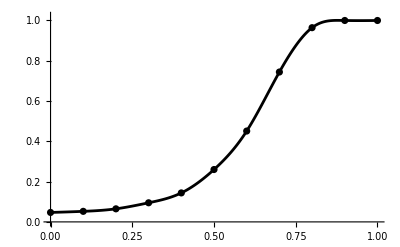

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02}];

plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}];

Show[plot1,plot2]
```

```mathematica
(*** Non-random sample sizes  ***)
```

```mathematica
n=42;
p1=5;
p2=11;
p22=4;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
P05nr42={0.0501,0.0558,0.0688,0.1066,0.1757,0.2962,0.5217,0.7924,0.9755,0.9999,1.};
```

0.33693947638704418822

```mathematica
n=100;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.69683032084243591833

```mathematica
n=60;
q05nr=BisecNRSEven[n,p1,p2,p22,0.0001,0.99,0.05]
```

0.51200920172347976488

```mathematica
n=32;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.18820501193517071839

```mathematica
n=20;
q05nr=BisecNRSEven[n,p1,p2,p22,0.00000001,0.99,0.05]
```

0.0075581343683621566057

```mathematica
(*** Computations for Power -- non-random sample sizes  ***)
P05nr={};
nv=10000;
Do[Mat=NMA[SIG,p1,p2,p22,d];
p=p1+p2;
L=Table[0,{j,1,nv}];
Do[X=RandomReal[MultinormalDistribution[Table[0,{j,1,p}],Mat],n];
A=Covariance[X];
L1=Det[A]/(Det[A[[(p1+1);;p,(p1+1);;p]]]);
L2=Det[A[[1;;(p-p22),1;;(p-p22)]]]/(Det[A[[(p1+1);;(p-p22),(p1+1);;(p-p22)]]]);
L[[i]]=L1/L2,{i,1,nv}];
P05nr=Append[P05nr,N[Count[L,x_/;x<q05nr]/nv]],{d,list}]
P05nr
```

{0.0468,0.0483,0.0502,0.0563,0.0624,0.0829,0.103,0.1482,0.2475,0.5206,0.9999}

```mathematica
P05nr100={0.0487,0.0597,0.131,0.2867,0.5674,0.8618,0.9876,0.9999,1.,1.,1.};
P05nr60={0.0493,0.0642,0.0874,0.1565,0.2897,0.5062,0.8014,0.969,0.9997,1.,1.};
P05nr32={0.0506,0.0529,0.0656,0.078,0.1216,0.188,0.309,0.5302,0.8337,0.9954,1.};
P05nr20={0.0468,0.0483,0.0502,0.0563,0.0624,0.0829,0.103,0.1482,0.2475,0.5206,0.9999};
```

```mathematica
(*** Plots of power *** Com labels nos eixos (eixo x - "δ values", eixo y - "power"***)
```

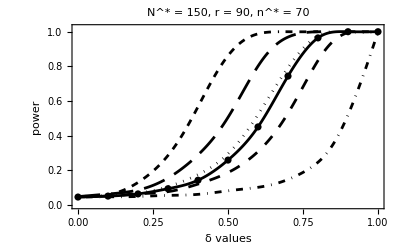

```mathematica
plot1=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},Joined->True,Joined->True,InterpolationOrder->3,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]}},PlotRange->{0,1.02},Frame->{{True,False},{True,False}},Axes->False,FrameLabel->{{Style["power",13,FontFamily->"Times New Roman"],None},{Style[Row[{TraditionalForm[δ]," values"}],13,FontFamily->"Times New Roman"],None}},PlotLabel->Style[Row[{Superscript[Style["N",Italic],"*"]," = 150, ",Style["r",Italic]," = 90, ",Superscript[Style["n",Italic],"*"]," = 70 "}],13,FontFamily->"Times New Roman"]];
plot2=ListPlot[{Table[{list[[i]],P05[[i]]},{i,1,Length[list]}]},PlotStyle->{Black}];
plot3=ListPlot[{Table[{list[[i]],P05nr20[[i]]},{i,1,Length[list]}],
Table[{list[[i]],P05nr32[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr42[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr60[[i]]},{i,1,Length[list]}],Table[{list[[i]],P05nr100[[i]]},{i,1,Length[list]}]},Joined->True,InterpolationOrder->6,PlotStyle->{{DotDashed,Black,Thickness[0.005]},{Dashing[{.02,.02}],Black,Thickness[0.005]},{Dotted,Black,Thickness[0.005]},{Dashing[{.04,.02}],Black,Thickness[0.005]},{Dashed,Black,Thickness[0.005]}},PlotRange->All];
Show[plot1,plot2,plot3]
```